## Network

```mathematica
net=NetChain[{LinearLayer[3,"Biases"->None,"Input"->3],LogisticSigmoid,LinearLayer[6,"Biases"->None],LogisticSigmoid,LinearLayer[3,"Biases"->None],LogisticSigmoid}];
net=NetInitialize[net]
```

NetChain[<>]

```mathematica
net[{0,1,0}]
```

{0.49651,0.606248,0.708361}

```mathematica
trainingData=Thread[#->RandomSample[#]]&@(IntegerDigits[#,2,3]&/@Range[7,0,-1])
```

{{1,1,1}→{1,1,1},{1,1,0}→{0,1,0},{1,0,1}→{1,0,1},{1,0,0}→{1,1,0},{0,1,1}→{0,0,1},{0,1,0}→{0,0,0},{0,0,1}→{0,1,1},{0,0,0}→{1,0,0}}

```mathematica
net=NetInitialize[net,All];
net=NetTrain[net,trainingData,Method->{"ADAM","L2Regularization"->0.001}]
```

NetChain[<>]

```mathematica
net[{1,1,0}]
```

{0.170989,0.842668,0.00195172}

```mathematica
TrainANet[initNet_,data_,n_]:=ParallelTable[NetTrain[NetInitialize[anet,All],data,Method->{"ADAM","L2Regularization"->0.001},TrainingProgressReporting->None],{anet,Table[initNet,n]}]
```

```mathematica
AbsoluteTiming[Quiet[TrainANet[net,trainingData,2]];]
```

{4.49369,Null}

```mathematica
AbsoluteTiming[TrainANet[net,trainingData,1];]
```

{4.47449,Null}

```mathematica
AbsoluteTiming[TrainANet[net,trainingData,6];]
```

{10.1854,Null}

```mathematica
AbsoluteTiming[TrainANet[net,trainingData,12];]
```

{20.8615,Null}

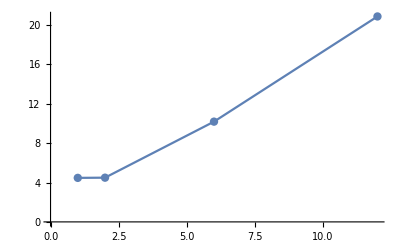

```mathematica
ListLinePlot[{{1,4.47},{2,4.49},{6,10.18},{12,20.86}},Mesh->Full]
```

```mathematica
netlist=TrainANet[net,trainingData,6]
```

{NetChain[<>],NetChain[<>],NetChain[<>],NetChain[<>],NetChain[<>],NetChain[<>]}

```mathematica
Table[Mean[Flatten[NetExtract[anet,{#,"Weights"}]&/@{1,3,5}]^2],{anet,netlist}]
```

{8.88701,8.4869,8.96641,8.61346,9.07557,8.83555}